```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\User\Desktop\GAS Market 2

```mathematica
FileNames[]
```

{ccListFull,consumptionProductionAssoc,exportAssoc,graphDB,import.nb,чистая обработка данных.nb,сравнение с нормой.nb,nrg_cb_gasm.tsv,nrg_ti_gasm.tsv,priceAssoc,Prices TZT.xlsx,result.xlsx,SSO_EIC.xls,storageDB,terminalDB,сравнение с нормой — копия.nb}

```mathematica
assocsNames=Select[FileNames[],StringFreeQ["."]]
```

```mathematica
{"ccListFull","consumptionProductionAssoc","exportAssoc","graphDB","priceAssoc","storageDB","terminalDB"}
```

```mathematica
With[{n=ToExpression@#},n=Get@#]&/@assocsNames;
```

```mathematica
ccListFull
```

{AE,AL,AM,AO,AR,AT,AU,AZ,BA,BE,BG,BN,BO,BY,CA,CH,CL,CM,CY,CZ,DE,DK,DZ,EE,EG,EL,ES,FI,FR,GE,GH,GI,GQ,HR,HU,ID,IE,IL,IQ,IR,IT,JO,JP,KP,KR,KZ,LB,LT,LU,LV,LY,MA,MD,ME,MK,MT,MX,MY,NG,NL,NO,NZ,OM,PE,PG,PL,PT,QA,RO,RS,RU,SE,SI,SK,SY,TM,TN,TR,TT,UA,UK,US,UZ,YE}

```mathematica
consumptionProductionAssoc//Keys
```

{consumption,production}

```mathematica
consumptionProductionAssoc["consumption","bcm","DE"]
```

<|Dec 2020→Missing[],Nov 2020→10.4642,Oct 2020→7.90157,Sep 2020→5.38538,Aug 2020→4.47173,Jul 2020→4.57385,Jun 2020→4.72494,May 2020→5.7756,Apr 2020→5.63109,Mar 2020→10.3654,Feb 2020→10.0526,Jan 2020→12.1983,Dec 2019→11.3031,Nov 2019→10.296,Oct 2019→7.59122,Sep 2019→5.45051,Aug 2019→4.20775,Jul 2019→5.51631,Jun 2019→3.78028,May 2019→6.38344,Apr 2019→6.80492,Mar 2019→9.89427,Feb 2019→11.1802,Jan 2019→13.6226,Dec 2018→7.92723,Nov 2018→10.1936,Oct 2018→7.32833,Sep 2018→4.98636,Aug 2018→4.62391,Jul 2018→4.38936,Jun 2018→4.99921,May 2018→4.95276,Apr 2018→6.29271,Mar 2018→10.8934,Feb 2018→11.975,Jan 2018→10.6111,Dec 2017→11.1231,Nov 2017→10.5022,Oct 2017→6.9821,Sep 2017→5.87288,Aug 2017→4.74593,Jul 2017→5.65716,Jun 2017→5.11621,May 2017→6.36031,Apr 2017→8.01764,Mar 2017→8.53838,Feb 2017→9.64981,Jan 2017→14.0263,Dec 2016→11.7249,Nov 2016→10.579,Oct 2016→7.49879,Sep 2016→4.53137,Aug 2016→4.5624,Jul 2016→4.55382,Jun 2016→4.18465,May 2016→5.54888,Apr 2016→6.11154,Mar 2016→9.89991,Feb 2016→10.3572,Jan 2016→13.452,Dec 2015→8.97438,Nov 2015→7.96148,Oct 2015→7.61597,Sep 2015→4.92993,Aug 2015→4.02971,Jul 2015→4.33187,Jun 2015→4.78706,May 2015→5.31829,Apr 2015→6.97694,Mar 2015→8.77107,Feb 2015→10.3197,Jan 2015→10.6604,Dec 2014→10.6423,Nov 2014→10.448,Oct 2014→6.39432,Sep 2014→4.91366,Aug 2014→3.99252,Jul 2014→5.45418,Jun 2014→4.15672,May 2014→6.28288,Apr 2014→4.79029,Mar 2014→7.41831,Feb 2014→7.7493,Jan 2014→9.86702,Dec 2013→10.0462,Nov 2013→7.9363,Oct 2013→4.81998,Sep 2013→6.08951,Aug 2013→5.04075,Jul 2013→4.48346,Jun 2013→4.68447,May 2013→5.5006,Apr 2013→8.24855,Mar 2013→13.2153,Feb 2013→10.8307,Jan 2013→11.3291,Dec 2012→Missing[],Nov 2012→Missing[],Oct 2012→Missing[],Sep 2012→Missing[],Aug 2012→Missing[],Jul 2012→Missing[],Jun 2012→Missing[],May 2012→Missing[],Apr 2012→Missing[],Mar 2012→Missing[],Feb 2012→Missing[],Jan 2012→Missing[],Dec 2011→Missing[],Nov 2011→Missing[],Oct 2011→Missing[],Sep 2011→Missing[],Aug 2011→Missing[],Jul 2011→Missing[],Jun 2011→Missing[],May 2011→Missing[],Apr 2011→Missing[],Mar 2011→Missing[],Feb 2011→Missing[],Jan 2011→Missing[],Dec 2010→Missing[],Nov 2010→Missing[],Oct 2010→Missing[],Sep 2010→Missing[],Aug 2010→Missing[],Jul 2010→Missing[],Jun 2010→Missing[],May 2010→Missing[],Apr 2010→Missing[],Mar 2010→Missing[],Feb 2010→Missing[],Jan 2010→Missing[],Dec 2009→Missing[],Nov 2009→Missing[],Oct 2009→Missing[],Sep 2009→Missing[],Aug 2009→Missing[],Jul 2009→Missing[],Jun 2009→Missing[],May 2009→Missing[],Apr 2009→Missing[],Mar 2009→Missing[],Feb 2009→Missing[],Jan 2009→Missing[],Dec 2008→Missing[],Nov 2008→Missing[],Oct 2008→Missing[],Sep 2008→Missing[],Aug 2008→Missing[],Jul 2008→Missing[],Jun 2008→Missing[],May 2008→Missing[],Apr 2008→Missing[],Mar 2008→Missing[],Feb 2008→Missing[],Jan 2008→Missing[]|>

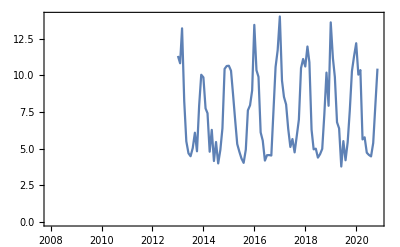

```mathematica
consumptionProductionAssoc["consumption","bcm","DE"]//DateListPlot
```

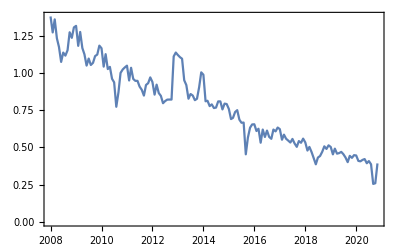

```mathematica
consumptionProductionAssoc["production","bcm","DE"]//DateListPlot
```

```mathematica
exportAssoc["bcm","DE"]//Keys
```

{AL,AT,BE,BG,CY,CZ,DE,DK,EA,EA19,EE,EL,ES,EU27_2007,EU27_2020,FI,FR,GE,HR,HU,IE,IS,IT,LT,LU,LV,MK,MT,NL,NO,PL,PT,RO,RS,SE,SI,SK,TR,UK}

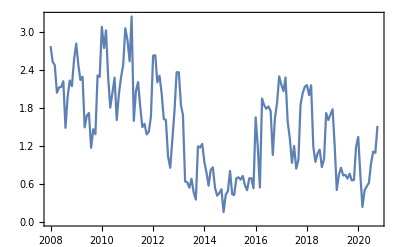

```mathematica
exportAssoc["bcm","DZ","IT"]//DateListPlot
```

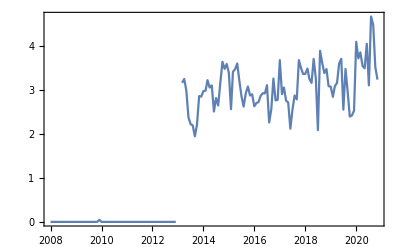

```mathematica
exportAssoc["bcm","DE","CZ"]//DateListPlot
```

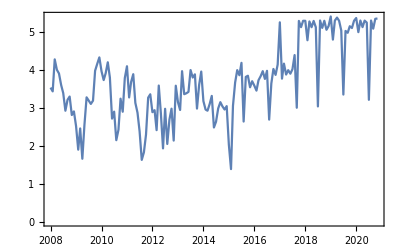

```mathematica
exportAssoc["bcm","RU","DE"]//DateListPlot
```

```mathematica
exportAssoc["bcm","DE","RU"]
```

Missing[KeyAbsent,RU]

```mathematica
exportAssoc["bcm","DE"]//Keys
```

{AL,AT,BE,BG,CY,CZ,DE,DK,EA,EA19,EE,EL,ES,EU27_2007,EU27_2020,FI,FR,GE,HR,HU,IE,IS,IT,LT,LU,LV,MK,MT,NL,NO,PL,PT,RO,RS,SE,SI,SK,TR,UK}

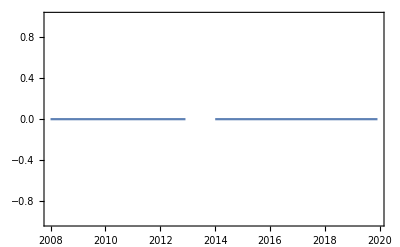

```mathematica
exportAssoc["bcm","DE","PT"]//DateListPlot
```

```mathematica
graphDB//Keys
```

{arcCapTimeAssoc,vertexCountryAssoc,arcList,tsoList,lngList,storList,exportDirections,consumVertexList,consumList,prodVertexList,prodList,exporterVertexList,exporterList}

```mathematica
graphDB["arcCapTimeAssoc",DateObject[{2019,1},"Month","Gregorian",3.]]
```

<|interconnector->fluxys belgium→20202.7,fluxys belgium->interconnector→24905.4,fluxys belgium->gts→8401.,gts->fluxys belgium→44541.8,fluxys belgium->zebra pijpleiding→3782.,gascade gastransport->fluxys belgium→4098.2,fluxys belgium->gascade gastransport→4014.5,open grid europe->fluxys belgium→8317.3,thyssengas->fluxys belgium→8317.3,fluxys tenp->fluxys belgium→8317.3,fluxys belgium->open grid europe→4960.,fluxys belgium->thyssengas→4960.,fluxys belgium->fluxys tenp→4960.,open grid europe->creos luxembourg→1190.4,fluxys belgium->grtgaz→26350.,gts->open grid europe→30325.1,gts->fluxys tenp→12269.8,gts->thyssengas→10372.5,gts->rwe→2232.,eneco->gts→2901.6,gts->eneco→1341.97,gts->innogy→1472.81,gascade gastransport->gts→9241.1,gasunie deutschland ->gts→1329.9,gts->gasunie deutschland →7592.06,open grid europe->gts→5028.2,gts->gastransport nord→2176.04,ewe gasspeicher->gts→2099.01,gts->ewe gasspeicher→1510.32,national grid gas->interconnector→20202.7,national grid gas->gni→14762.2,national grid gas->premier transmission→14762.2,gas connect austria->open grid europe→4956.9,gas connect austria->grtgaz deutschland→4956.9,open grid europe->gas connect austria→6181.4,grtgaz deutschland->gas connect austria→6181.4,open grid europe->grtgaz→18776.7,grtgaz deutschland->grtgaz→18776.7,gas connect austria->bayernets→5412.6,bayernets->gas connect austria→3534.,gas connect austria->plinovodi→3487.5,tag->snam rete gas→35612.8,snam rete gas->tag→5992.3,fluxswiss->snam rete gas→19697.4,swissgas->snam rete gas→19697.4,snam rete gas->fluxswiss→13283.5,snam rete gas->swissgas→13283.5,fluxswiss->fluxys tenp→5356.8,fluxswiss->open grid europe→5356.8,fluxys tenp->fluxswiss→9856.14,fluxys tenp->swissgas→9856.14,open grid europe->fluxswiss→9856.14,open grid europe->swissgas→9856.14,snam rete gas->plinovodi→877.3,plinovodi->snam rete gas→663.4,plinacro ltd->plinovodi→238.7,plinovodi->plinacro ltd→1664.7,fluxswiss->grtgaz→3100.,swissgas->grtgaz→3100.,grtgaz->fluxswiss→6913.,grtgaz->swissgas→6913.,open grid europe->energinet→5161.5,gasunie deutschland ->energinet→5161.5,energinet->open grid europe→2821.,energinet->gasunie deutschland →2821.,gascade gastransport->gaz-system (iso)→5728.8,gaz-system (iso)->gascade gastransport→28876.5,net4gas->gascade gastransport→5685.4,gascade gastransport->net4gas→11156.9,net4gas->ontras→462.653,ontras->net4gas→2946.24,opal gastransport->net4gas→59016.2,lbtg->net4gas→29508.1,net4gas->open grid europe→28113.9,net4gas->grtgaz deutschland→28113.9,net4gas->gaz-system→868.,net4gas->eustream→28324.7,eustream->net4gas→12412.4,gas connect austria->eustream→22924.5,tag->eustream→7641.5,eustream->gas connect austria→97364.8,eustream->tag→48682.4,gas connect austria->fgsz→4746.1,fgsz->srbijagas→4402.,srbijagas->bh gas→557.38,bulgartransgaz->ga-ma - skopje→631.78,bulgartransgaz->desfa→3628.55,desfa->bulgartransgaz→1442.43,bulgartransgaz->botas→14787.,transgaz->bulgartransgaz→39419.6,conexus->elering→5208.,amber grid->conexus→2095.6,conexus->amber grid→2018.1,amber grid->gazprom→3540.2,fgsz->transgaz→1615.1,transgaz->fgsz→77.5,fgsz->plinacro ltd→2427.3,eustream->spp storage→2304.54,spp storage->eustream→2962.98,gas connect austria->nafta→4287.3,gas connect austria->pozagas→4287.3,nafta->gas connect austria→4287.3,pozagas->gas connect austria→4287.3,bayernets->rag→168.144,rag->bayernets→31.,bayernets->astora→8300.56,bayernets->gsa llc→8300.56,astora->bayernets→9298.31,gsa llc->bayernets→9298.31,enagas->ren - gasodutos→4464.,ren - gasodutos->enagas→2480.,grtgaz->gaznat→1159.4,eustream->pjsc ukrtransgaz→12896.,pjsc ukrtransgaz->eustream→259210.,transgaz->vestmoldtransgaz→40.3,eustream->mgt→3935.92,enagas->teréga→6956.4,teréga->enagas→5115.,terranets bw->gvm→272.8,terranets bw->vorarlberger erdgas→787.4,elering->gazprom→3255.,gazprom->elering→6640.2,ontras->gaz-system→1509.7,gaz-system->ontras→3.1,bulgartransgaz->transgaz→244.9,grtgaz->fluxys belgium→8370.,gassco->national grid gas→46472.1,gassco->gasunie deutschland →59032.,gassco->jordgas transport→13103.7,gassco->open grid europe→59032.,gassco->gts→45928.3,gassco->thyssengas→45928.3,gassco->fluxys belgium→15128.,gassco->grtgaz→17670.,empl->enagas→13723.7,medgaz->enagas→8959.,tmpc->snam rete gas→35659.3,green stream->snam rete gas→15469.,gazprom->gasum oy→6820.,elering->conexus→5533.5,gazprom belarus->amber grid→10087.4,gazprom belarus->gaz-system→5468.4,gazprom belarus->gaz-system (iso)→31753.3,pjsc ukrtransgaz->gaz-system→4203.6,pjsc ukrtransgaz->fgsz→16014.6,pjsc ukrtransgaz->transgaz→34537.1,botas->igi poseidon→1506.29,botas->desfa→1506.29,nord stream->lbtg→108004.,nord stream->opal gastransport→108004.,nord stream->fluxys deutschland→54002.,nord stream->gasunie deutschland →54002.,nord stream->goal→54002.,nord stream->nel gastransport→54002.,fgsz->pjsc ukrtransgaz→0.,dong->energinet→12276.,gascade gastransport->open grid europe→2526.5,gascade gastransport->thyssengas→148.8,gascade gastransport->terranets bw→849.4,gasunie deutschland ->thyssengas→204.6,ontras->open grid europe→2064.6,open grid europe->ontras→1066.4,gascade gastransport->grtgaz deutschland→3304.6,gaz-system (iso)->gaz-system→8540.5,gasunie deutschland ->open grid europe→1121.27,premier transmission->gni (uk)→1302.,fgsz->mgt→1595.26,mgt->fgsz→4011.09,fluxys belgium->creos luxembourg→1512.8,zeebrugge lng->fluxys belgium→14787.,isle of grain->national grid gas→19377.1,milford haven->national grid gas→56839.6,montoir de bretagne->grtgaz→9936.99,fos (tonkin/cavaou)->grtgaz→22358.2,panigaglia->snam rete gas→3685.9,cavarzere (porto levante / adriatic lng)->itg→7532.22,cavarzere (porto levante / adriatic lng)->snam rete gas→7532.22,agia triada->desfa→6338.88,barcelona->enagas→16829.9,sagunto->enagas→8627.3,cartagena->enagas→11649.8,huelva->enagas→11649.8,mugardos->reganosa→3571.2,bilbao->enagas→6903.7,sines->ren - gasodutos→6200.,sines->ren atlantico→155.,gate terminal (i)->gts→11924.4,olt lng / livorno->snam rete gas→3776.05,klaipeda (lng)->amber grid→3794.4,dunkerque lng->grtgaz→17670.,swinoujscie->gaz-system→4898.,nptf->energinet→∞,energinet->nptf→∞,gtf (bilateral trading point)->energinet→∞,energinet->gtf (bilateral trading point)→∞,ttf->gts→∞,gts->ttf→∞,vhp gaspool->fluxys deutschland→∞,vhp gaspool->gascade gastransport→∞,vhp gaspool->gastransport nord→∞,vhp gaspool->gasunie deutschland →∞,vhp gaspool->jordgas transport→∞,vhp gaspool->nel gastransport→∞,vhp gaspool->nowega→∞,vhp gaspool->ontras→∞,vhp gaspool->opal gastransport→∞,fluxys deutschland->vhp gaspool→∞,gascade gastransport->vhp gaspool→∞,gastransport nord->vhp gaspool→∞,gasunie deutschland ->vhp gaspool→∞,jordgas transport->vhp gaspool→∞,nel gastransport->vhp gaspool→∞,nowega->vhp gaspool→∞,ontras->vhp gaspool→∞,opal gastransport->vhp gaspool→∞,vhp netconnectgermany->bayernets→∞,vhp netconnectgermany->fluxys tenp→∞,vhp netconnectgermany->grtgaz deutschland→∞,vhp netconnectgermany->open grid europe→∞,vhp netconnectgermany->terranets bw→∞,vhp netconnectgermany->thyssengas→∞,bayernets->vhp netconnectgermany→∞,fluxys tenp->vhp netconnectgermany→∞,grtgaz deutschland->vhp netconnectgermany→∞,open grid europe->vhp netconnectgermany→∞,terranets bw->vhp netconnectgermany→∞,thyssengas->vhp netconnectgermany→∞,ote->net4gas→∞,net4gas->ote→∞,nbp->national grid gas→∞,national grid gas->nbp→∞,ibp->gni→∞,gni->ibp→∞,peg->grtgaz→∞,peg->teréga→∞,grtgaz->peg→∞,teréga->peg→∞,psv->snam rete gas→∞,snam rete gas->psv→∞,pvb->enagas→∞,enagas->pvb→∞,mgp->fgsz→∞,fgsz->mgp→∞,cegh->gas connect austria→∞,cegh->tag→∞,gas connect austria->cegh→∞,tag->cegh→∞,ztp (zeebrugge trading point h-zone)->fluxys belgium→∞,fluxys belgium->ztp (zeebrugge trading point h-zone)→∞,vtp - gaz-system->gaz-system→∞,gaz-system->vtp - gaz-system→∞,zeebrugge beach->fluxys belgium→∞,fluxys belgium->zeebrugge beach→∞,htp (hellenic trading point)->desfa→∞,desfa->htp (hellenic trading point)→∞,ren - gasodutos->reganosa→∞,reganosa->ren - gasodutos→∞,gazprom->gazprom belarus→∞,gazprom belarus->gazprom→∞,gazprom->pjsc ukrtransgaz→∞,pjsc ukrtransgaz->gazprom→∞,IR-tso->botas→∞,AZ-tso->botas→∞,gazprom->botas→∞,SE-tso->energinet→∞,energinet->SE-tso→∞|>

```mathematica
graphDB["vertexCountryAssoc"]
```

<|fluxys belgium→BE,interconnector→UK,gts→NL,zebra pijpleiding→NL,gascade gastransport→DE,open grid europe→DE,thyssengas→DE,fluxys tenp→DE,creos luxembourg→LU,grtgaz→FR,rwe→DE,eneco→DE,innogy→DE,gasunie deutschland →DE,gastransport nord→DE,ewe gasspeicher→DE,national grid gas→UK,gni→IE,premier transmission→UK,gas connect austria→AT,grtgaz deutschland→DE,bayernets→DE,plinovodi→SI,snam rete gas→IT,tag→AT,fluxswiss→CH,swissgas→CH,plinacro ltd→HR,energinet→DK,gaz-system (iso)→PL,net4gas→CZ,ontras→DE,opal gastransport→DE,lbtg→DE,gaz-system→PL,eustream→SK,fgsz→HU,srbijagas→RS,bh gas→BA,ga-ma - skopje→MK,bulgartransgaz→BG,desfa→EL,botas→TR,transgaz→RO,elering→EE,conexus→LV,amber grid→LT,gazprom→RU,spp storage→CZ,nafta→SK,pozagas→SK,rag→AT,astora→AT,gsa llc→AT,ren - gasodutos→PT,enagas→ES,gaznat→CH,pjsc ukrtransgaz→RU,vestmoldtransgaz→MD,mgt→HU,teréga→FR,gvm→CH,terranets bw→DE,vorarlberger erdgas→AT,gassco→NO,jordgas transport→DE,empl→DZ,medgaz→DZ,tmpc→DZ,green stream→LY,gasum oy→FI,gazprom belarus→RU,igi poseidon→EL,nord stream→RU,fluxys deutschland→DE,goal→DE,nel gastransport→DE,dong→NO,gni (uk)→UK,zeebrugge lng→BE,isle of grain→UK,milford haven→UK,montoir de bretagne→FR,fos (tonkin/cavaou)→FR,panigaglia→IT,itg→IT,cavarzere (porto levante / adriatic lng)→IT,agia triada→EL,barcelona→ES,sagunto→ES,cartagena→ES,huelva→ES,reganosa→ES,mugardos→ES,bilbao→ES,sines→PT,ren atlantico→PT,gate terminal (i)→NL,olt lng / livorno→IT,klaipeda (lng)→LT,dunkerque lng→FR,swinoujscie→PL,nptf→DK,gtf (bilateral trading point)→DK,ttf→NL,vhp gaspool→DE,nowega→DE,vhp netconnectgermany→DE,ote→CZ,nbp→UK,ibp→IE,peg→FR,psv→IT,pvb→ES,mgp→HU,cegh→AT,ztp (zeebrugge trading point h-zone)→BE,vtp - gaz-system→PL,zeebrugge beach→BE,htp (hellenic trading point)→EL,IR-tso→IR,AZ-tso→AZ,SE-tso→SE,UGS AT→AT,UGS BE→BE,UGS BG→BG,UGS CZ→CZ,UGS DE→DE,UGS DK→DK,UGS ES→ES,UGS FR→FR,UGS UK→UK,UGS HR→HR,UGS HU→HU,UGS IE→IE,UGS IT→IT,UGS LV→LV,UGS NL→NL,UGS PL→PL,UGS PT→PT,UGS RO→RO,UGS SE→SE,UGS SK→SK,UGS UA→RU|>

```mathematica
graphDB["arcList"]
```

{agia triada->desfa,amber grid->conexus,amber grid->consum LT,amber grid->gazprom,astora->bayernets,astora->consum AT,astora->UGS AT,AZ-tso->botas,barcelona->enagas,bayernets->astora,bayernets->consum DE,bayernets->gas connect austria,bayernets->gsa llc,bayernets->rag,bayernets->UGS DE,bilbao->enagas,botas->consum TR,botas->desfa,botas->igi poseidon,bulgartransgaz->botas,bulgartransgaz->consum BG,bulgartransgaz->desfa,bulgartransgaz->ga-ma - skopje,bulgartransgaz->transgaz,bulgartransgaz->UGS BG,cartagena->enagas,cavarzere (porto levante / adriatic lng)->itg,cavarzere (porto levante / adriatic lng)->snam rete gas,conexus->amber grid,conexus->consum LV,conexus->elering,conexus->UGS LV,creos luxembourg->consum LU,desfa->bulgartransgaz,desfa->consum EL,dong->energinet,dunkerque lng->grtgaz,elering->conexus,elering->consum EE,elering->gazprom,empl->enagas,enagas->consum ES,enagas->ren - gasodutos,enagas->teréga,enagas->UGS ES,eneco->consum DE,eneco->gts,eneco->UGS DE,energinet->consum DK,energinet->gasunie deutschland ,energinet->open grid europe,energinet->SE-tso,energinet->UGS DK,eustream->consum SK,eustream->gas connect austria,eustream->mgt,eustream->net4gas,eustream->pjsc ukrtransgaz,eustream->spp storage,eustream->tag,eustream->UGS SK,ewe gasspeicher->consum DE,ewe gasspeicher->gts,ewe gasspeicher->UGS DE,export AZ->AZ-tso,export DZ->empl,export DZ->medgaz,export DZ->tmpc,export IR->IR-tso,export LY->green stream,export NO->dong,export NO->gassco,export RU->gazprom,export RU->nord stream,fgsz->consum HU,fgsz->mgt,fgsz->pjsc ukrtransgaz,fgsz->plinacro ltd,fgsz->srbijagas,fgsz->transgaz,fgsz->UGS HU,fluxswiss->fluxys tenp,fluxswiss->grtgaz,fluxswiss->open grid europe,fluxswiss->snam rete gas,fluxys belgium->consum BE,fluxys belgium->creos luxembourg,fluxys belgium->fluxys tenp,fluxys belgium->gascade gastransport,fluxys belgium->grtgaz,fluxys belgium->gts,fluxys belgium->interconnector,fluxys belgium->open grid europe,fluxys belgium->thyssengas,fluxys belgium->UGS BE,fluxys belgium->zebra pijpleiding,fluxys deutschland->consum DE,fluxys deutschland->UGS DE,fluxys tenp->consum DE,fluxys tenp->fluxswiss,fluxys tenp->fluxys belgium,fluxys tenp->swissgas,fluxys tenp->UGS DE,fos (tonkin/cavaou)->grtgaz,ga-ma - skopje->consum MK,gascade gastransport->consum DE,gascade gastransport->fluxys belgium,gascade gastransport->gaz-system (iso),gascade gastransport->grtgaz deutschland,gascade gastransport->gts,gascade gastransport->net4gas,gascade gastransport->open grid europe,gascade gastransport->terranets bw,gascade gastransport->thyssengas,gascade gastransport->UGS DE,gas connect austria->bayernets,gas connect austria->consum AT,gas connect austria->eustream,gas connect austria->fgsz,gas connect austria->grtgaz deutschland,gas connect austria->nafta,gas connect austria->open grid europe,gas connect austria->plinovodi,gas connect austria->pozagas,gas connect austria->UGS AT,gassco->fluxys belgium,gassco->gasunie deutschland ,gassco->grtgaz,gassco->gts,gassco->jordgas transport,gassco->national grid gas,gassco->open grid europe,gassco->thyssengas,gastransport nord->consum DE,gastransport nord->UGS DE,gasum oy->consum FI,gasunie deutschland ->consum DE,gasunie deutschland ->energinet,gasunie deutschland ->gts,gasunie deutschland ->open grid europe,gasunie deutschland ->thyssengas,gasunie deutschland ->UGS DE,gate terminal (i)->gts,gazprom->botas,gazprom->elering,gazprom->gasum oy,gazprom->gazprom belarus,gazprom->pjsc ukrtransgaz,gazprom belarus->amber grid,gazprom belarus->gazprom,gazprom belarus->gaz-system,gazprom belarus->gaz-system (iso),gaz-system->consum PL,gaz-system->ontras,gaz-system->UGS PL,gaz-system (iso)->consum PL,gaz-system (iso)->gascade gastransport,gaz-system (iso)->gaz-system,gaz-system (iso)->UGS PL,gni->consum IE,gni->UGS IE,gni (uk)->consum UK,gni (uk)->UGS UK,goal->consum DE,goal->UGS DE,green stream->snam rete gas,grtgaz->consum FR,grtgaz->fluxswiss,grtgaz->fluxys belgium,grtgaz->gaznat,grtgaz->swissgas,grtgaz->UGS FR,grtgaz deutschland->consum DE,grtgaz deutschland->gas connect austria,grtgaz deutschland->grtgaz,grtgaz deutschland->UGS DE,gsa llc->bayernets,gsa llc->consum AT,gsa llc->UGS AT,gts->consum NL,gts->eneco,gts->ewe gasspeicher,gts->fluxys belgium,gts->fluxys tenp,gts->gastransport nord,gts->gasunie deutschland ,gts->innogy,gts->open grid europe,gts->rwe,gts->thyssengas,gts->UGS NL,huelva->enagas,igi poseidon->consum EL,innogy->consum DE,innogy->UGS DE,interconnector->consum UK,interconnector->fluxys belgium,interconnector->UGS UK,IR-tso->botas,isle of grain->national grid gas,itg->consum IT,itg->UGS IT,jordgas transport->consum DE,jordgas transport->UGS DE,klaipeda (lng)->amber grid,lbtg->consum DE,lbtg->net4gas,lbtg->UGS DE,medgaz->enagas,mgt->consum HU,mgt->fgsz,mgt->UGS HU,milford haven->national grid gas,montoir de bretagne->grtgaz,mugardos->reganosa,nafta->consum SK,nafta->gas connect austria,nafta->UGS SK,national grid gas->consum UK,national grid gas->gni,national grid gas->interconnector,national grid gas->premier transmission,national grid gas->UGS UK,nel gastransport->consum DE,nel gastransport->UGS DE,net4gas->consum CZ,net4gas->eustream,net4gas->gascade gastransport,net4gas->gaz-system,net4gas->grtgaz deutschland,net4gas->ontras,net4gas->open grid europe,net4gas->UGS CZ,nord stream->fluxys deutschland,nord stream->gasunie deutschland ,nord stream->goal,nord stream->lbtg,nord stream->nel gastransport,nord stream->opal gastransport,nowega->consum DE,nowega->UGS DE,olt lng / livorno->snam rete gas,ontras->consum DE,ontras->gaz-system,ontras->net4gas,ontras->open grid europe,ontras->UGS DE,opal gastransport->consum DE,opal gastransport->net4gas,opal gastransport->UGS DE,open grid europe->consum DE,open grid europe->creos luxembourg,open grid europe->energinet,open grid europe->fluxswiss,open grid europe->fluxys belgium,open grid europe->gas connect austria,open grid europe->grtgaz,open grid europe->gts,open grid europe->ontras,open grid europe->swissgas,open grid europe->UGS DE,panigaglia->snam rete gas,pjsc ukrtransgaz->eustream,pjsc ukrtransgaz->fgsz,pjsc ukrtransgaz->gazprom,pjsc ukrtransgaz->gaz-system,pjsc ukrtransgaz->transgaz,pjsc ukrtransgaz->UGS UA,plinacro ltd->consum HR,plinacro ltd->plinovodi,plinacro ltd->UGS HR,plinovodi->consum SI,plinovodi->plinacro ltd,plinovodi->snam rete gas,pozagas->consum SK,pozagas->gas connect austria,pozagas->UGS SK,premier transmission->consum UK,premier transmission->gni (uk),premier transmission->UGS UK,prod AT->astora,prod AT->gas connect austria,prod AT->gsa llc,prod AT->rag,prod AT->tag,prod AT->vorarlberger erdgas,prod BE->fluxys belgium,prod BG->bulgartransgaz,prod CZ->net4gas,prod CZ->spp storage,prod DE->bayernets,prod DE->eneco,prod DE->ewe gasspeicher,prod DE->fluxys deutschland,prod DE->fluxys tenp,prod DE->gascade gastransport,prod DE->gastransport nord,prod DE->gasunie deutschland ,prod DE->goal,prod DE->grtgaz deutschland,prod DE->innogy,prod DE->jordgas transport,prod DE->lbtg,prod DE->nel gastransport,prod DE->nowega,prod DE->ontras,prod DE->opal gastransport,prod DE->open grid europe,prod DE->rwe,prod DE->terranets bw,prod DE->thyssengas,prod DK->energinet,prod EL->desfa,prod EL->igi poseidon,prod ES->enagas,prod ES->reganosa,prod FR->grtgaz,prod FR->teréga,prod HR->plinacro ltd,prod HU->fgsz,prod HU->mgt,prod IE->gni,prod IT->itg,prod IT->snam rete gas,prod NL->gts,prod NL->zebra pijpleiding,prod PL->gaz-system,prod PL->gaz-system (iso),prod RO->transgaz,prod RS->srbijagas,prod SI->plinovodi,prod SK->eustream,prod SK->nafta,prod SK->pozagas,prod TR->botas,prod UK->gni (uk),prod UK->interconnector,prod UK->national grid gas,prod UK->premier transmission,rag->bayernets,rag->consum AT,rag->UGS AT,reganosa->consum ES,reganosa->ren - gasodutos,reganosa->UGS ES,ren atlantico->consum PT,ren atlantico->UGS PT,ren - gasodutos->consum PT,ren - gasodutos->enagas,ren - gasodutos->reganosa,ren - gasodutos->UGS PT,rwe->consum DE,rwe->UGS DE,sagunto->enagas,SE-tso->consum SE,SE-tso->energinet,SE-tso->UGS SE,sines->ren atlantico,sines->ren - gasodutos,snam rete gas->consum IT,snam rete gas->fluxswiss,snam rete gas->plinovodi,snam rete gas->swissgas,snam rete gas->tag,snam rete gas->UGS IT,spp storage->consum CZ,spp storage->eustream,spp storage->UGS CZ,srbijagas->bh gas,srbijagas->consum RS,swinoujscie->gaz-system,swissgas->grtgaz,swissgas->snam rete gas,tag->consum AT,tag->eustream,tag->snam rete gas,tag->UGS AT,teréga->consum FR,teréga->enagas,teréga->UGS FR,terranets bw->consum DE,terranets bw->gvm,terranets bw->UGS DE,terranets bw->vorarlberger erdgas,thyssengas->consum DE,thyssengas->fluxys belgium,thyssengas->UGS DE,tmpc->snam rete gas,transgaz->bulgartransgaz,transgaz->consum RO,transgaz->fgsz,transgaz->UGS RO,transgaz->vestmoldtransgaz,UGS AT->astora,UGS AT->gas connect austria,UGS AT->gsa llc,UGS AT->rag,UGS AT->tag,UGS AT->vorarlberger erdgas,UGS BE->fluxys belgium,UGS BG->bulgartransgaz,UGS CZ->net4gas,UGS CZ->spp storage,UGS DE->bayernets,UGS DE->eneco,UGS DE->ewe gasspeicher,UGS DE->fluxys deutschland,UGS DE->fluxys tenp,UGS DE->gascade gastransport,UGS DE->gastransport nord,UGS DE->gasunie deutschland ,UGS DE->goal,UGS DE->grtgaz deutschland,UGS DE->innogy,UGS DE->jordgas transport,UGS DE->lbtg,UGS DE->nel gastransport,UGS DE->nowega,UGS DE->ontras,UGS DE->opal gastransport,UGS DE->open grid europe,UGS DE->rwe,UGS DE->terranets bw,UGS DE->thyssengas,UGS DK->energinet,UGS ES->enagas,UGS ES->reganosa,UGS FR->grtgaz,UGS FR->teréga,UGS HR->plinacro ltd,UGS HU->fgsz,UGS HU->mgt,UGS IE->gni,UGS IT->itg,UGS IT->snam rete gas,UGS LV->conexus,UGS NL->gts,UGS NL->zebra pijpleiding,UGS PL->gaz-system,UGS PL->gaz-system (iso),UGS PT->ren atlantico,UGS PT->ren - gasodutos,UGS RO->transgaz,UGS SE->SE-tso,UGS SK->eustream,UGS SK->nafta,UGS SK->pozagas,UGS UA->pjsc ukrtransgaz,UGS UK->gni (uk),UGS UK->interconnector,UGS UK->national grid gas,UGS UK->premier transmission,vestmoldtransgaz->consum MD,vorarlberger erdgas->consum AT,vorarlberger erdgas->UGS AT,zebra pijpleiding->consum NL,zebra pijpleiding->UGS NL,zeebrugge lng->fluxys belgium}

```mathematica
graphDB["tsoList"]
graphDB["lngList"]
graphDB["storList"]
```

{amber grid,astora,bayernets,bh gas,botas,bulgartransgaz,conexus,creos luxembourg,desfa,dong,elering,empl,enagas,eneco,energinet,eustream,ewe gasspeicher,fgsz,fluxswiss,fluxys belgium,fluxys deutschland,fluxys tenp,ga-ma - skopje,gascade gastransport,gas connect austria,gassco,gastransport nord,gasum oy,gasunie deutschland ,gaznat,gazprom,gazprom belarus,gaz-system,gaz-system (iso),gni,gni (uk),goal,green stream,grtgaz,grtgaz deutschland,gsa llc,gts,gvm,igi poseidon,innogy,interconnector,itg,jordgas transport,lbtg,medgaz,mgt,nafta,national grid gas,nel gastransport,net4gas,nord stream,nowega,ontras,opal gastransport,open grid europe,pjsc ukrtransgaz,plinacro ltd,plinovodi,pozagas,premier transmission,rag,reganosa,ren atlantico,ren - gasodutos,rwe,snam rete gas,spp storage,srbijagas,swissgas,tag,teréga,terranets bw,thyssengas,tmpc,transgaz,vestmoldtransgaz,vorarlberger erdgas,zebra pijpleiding,IR-tso,SE-tso,AZ-tso}

{zeebrugge lng,isle of grain,milford haven,montoir de bretagne,fos (tonkin/cavaou),panigaglia,cavarzere (porto levante / adriatic lng),agia triada,barcelona,sagunto,cartagena,huelva,mugardos,bilbao,sines,gate terminal (i),olt lng / livorno,klaipeda (lng),dunkerque lng,swinoujscie}

{UGS AT,UGS BE,UGS BG,UGS CZ,UGS DE,UGS DK,UGS ES,UGS FR,UGS UK,UGS HR,UGS HU,UGS IE,UGS IT,UGS LV,UGS NL,UGS PL,UGS PT,UGS RO,UGS SE,UGS SK,UGS UA}

```mathematica
graphDB["exportDirections"]
```

<|RU→{DE,EE,FI,HU,LT,PL,RO,SK,TR},DZ→{ES,IT},NO→{BE,DE,FR,DK,NL,UK},AZ→{TR},LY→{IT},IR→{TR}|>

```mathematica
graphDB["consumVertexList"]
graphDB["consumList"]
```

{consum AT,consum BE,consum BG,consum CZ,consum DE,consum DK,consum EE,consum EL,consum ES,consum FI,consum FR,consum HR,consum HU,consum IE,consum IT,consum LT,consum LU,consum LV,consum MD,consum MK,consum NL,consum PL,consum PT,consum RO,consum RS,consum SE,consum SI,consum SK,consum TR,consum UK}

{AT,BE,BG,CZ,DE,DK,EE,EL,ES,FI,FR,HR,HU,IE,IT,LT,LU,LV,MD,MK,NL,PL,PT,RO,RS,SE,SI,SK,TR,UK}

```mathematica
graphDB["prodVertexList"]
graphDB["prodList"]
```

{prod AT,prod BE,prod BG,prod CZ,prod DE,prod DK,prod EL,prod ES,prod FR,prod HR,prod HU,prod IE,prod IT,prod NL,prod PL,prod RO,prod RS,prod SI,prod SK,prod TR,prod UK}

{AT,BE,BG,CZ,DE,DK,EL,ES,FR,HR,HU,IE,IT,NL,PL,RO,RS,SI,SK,TR,UK}

```mathematica
graphDB@"exporterVertexList"
graphDB@"exporterList"
```

{export RU,export DZ,export LY,export NO,export IR,export AZ}

{RU,DZ,LY,NO,IR,AZ}

```mathematica
priceAssoc
```

<|TTFG1MON Index→<|Jan 2016→13841.1,Feb 2016→12191.4,Mar 2016→12008.1,Apr 2016→11891.7,May 2016→13095.2,Jun 2016→14376.7,Jul 2016→14328.2,Aug 2016→12133.9,Sep 2016→12854.2,Oct 2016→16350.8,Nov 2016→17945.8,Dec 2016→17545.2,Jan 2017→19746.,Feb 2017→19393.8,Mar 2017→15987.1,Apr 2017→15919.2,May 2017→15571.,Jun 2017→14851.8,Jul 2017→14814.8,Aug 2017→15837.1,Sep 2017→16955.8,Oct 2017→17887.1,Nov 2017→19429.2,Dec 2017→20464.9,Jan 2018→18654.4,Feb 2018→18646.9,Mar 2018→18516.1,Apr 2018→19295.,May 2018→21524.2,Jun 2018→21726.7,Jul 2018→22144.4,Aug 2018→23803.2,Sep 2018→27694.2,Oct 2018→26119.4,Nov 2018→24815.,Dec 2018→23950.,Jan 2019→21854.8,Feb 2019→18090.2,Mar 2019→15628.4,Apr 2019→15013.3,May 2019→13296.,Jun 2019→10726.8,Jul 2019→9425.,Aug 2019→9425.,Sep 2019→12039.2,Oct 2019→15558.9,Nov 2019→15890.8,Dec 2019→14088.2,Jan 2020→11298.1,Feb 2020→9144.31,Mar 2020→8370.65,Apr 2020→6673.67,May 2020→4899.35,Jun 2020→5320.83,Jul 2020→5320.16,Aug 2020→8018.39,Sep 2020→11387.3,Oct 2020→14171.5,Nov 2020→13949.7,Dec 2020→15135.|>,CO1 Comdty→<|Jan 2016→32553.9,Feb 2016→33625.2,Mar 2016→39913.5,Apr 2016→43196.7,May 2016→47704.5,Jun 2016→49797.3,Jul 2016→46547.4,Aug 2016→47378.7,Sep 2016→47076.3,Oct 2016→51225.8,Nov 2016→46819.7,Dec 2016→54952.9,Jan 2017→55650.3,Feb 2017→56091.1,Mar 2017→52517.7,Apr 2017→53791.7,May 2017→51399.4,Jun 2017→47606.7,Jul 2017→49043.9,Aug 2017→52010.,Sep 2017→55379.,Oct 2017→57670.3,Nov 2017→62913.,Dec 2017→64259.7,Jan 2018→69027.1,Feb 2018→65773.2,Mar 2018→66925.5,Apr 2018→71802.,May 2018→76936.5,Jun 2018→75956.3,Jul 2018→75096.1,Aug 2018→73732.3,Sep 2018→78997.,Oct 2018→80595.5,Nov 2018→66267.3,Dec 2018→57332.9,Jan 2019→60092.3,Feb 2019→64466.8,Mar 2019→66914.8,Apr 2019→71606.3,May 2019→70377.7,Jun 2019→63461.3,Jul 2019→64216.1,Aug 2019→59557.1,Sep 2019→62145.3,Oct 2019→59747.7,Nov 2019→62703.7,Dec 2019→65358.1,Jan 2020→64033.5,Feb 2020→55757.6,Mar 2020→34020.,Apr 2020→27365.3,May 2020→32302.9,Jun 2020→40849.3,Jul 2020→43198.4,Aug 2020→44813.5,Sep 2020→41878.,Oct 2020→41439.7,Nov 2020→43726.,Dec 2020→49268.7|>|>

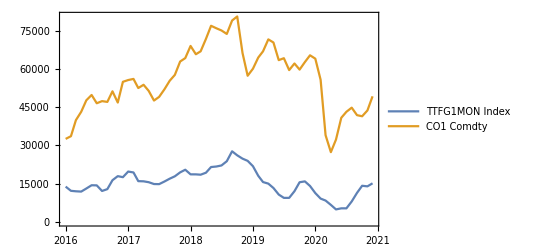

```mathematica
priceAssoc//DateListPlot
```

```mathematica
storageDB//Keys
```

{disaggregated,aggregated}

```mathematica
storageDB["aggregated","UGS DE"]//Keys
```

{CC,DayData,MonthData}

```mathematica
storageDB["aggregated","UGS DE","CC"]
storageDB["aggregated","UGS DE","MonthData"]⟦;;2⟧
```

DE

<|Dec 2015→<|gasInStorage→165500.,workingGasVolume→209349.,injection→62.99,injectionCapacity→3046.77,withdrawal→248.64,withdrawalCapacity→5648.83|>,Jan 2016→<|gasInStorage→139924.,workingGasVolume→209349.,injection→752.2,injectionCapacity→94429.2,withdrawal→26332.4,withdrawalCapacity→175114.|>|>

```mathematica
terminalDB//Keys
```

{zeebrugge lng,bilbao,barcelona,cartagena,huelva,sagunto,mugardos,montoir de bretagne,dunkerque lng,isle of grain,milford haven,agia triada,panigaglia,olt lng / livorno,cavarzere (porto levante / adriatic lng),klaipeda (lng),gate terminal (i),swinoujscie,sines,fos (tonkin/cavaou)}

```mathematica
terminalDB["zeebrugge lng","CC"]
terminalDB["zeebrugge lng","MonthData"]⟦;;5⟧
```

BE

<|Dec 2015→<|sendOut→22.,dtrs→444.5|>,Jan 2016→<|sendOut→961.6,dtrs→13779.5|>,Feb 2016→<|sendOut→1141.4,dtrs→12890.5|>,Mar 2016→<|sendOut→1101.,dtrs→13779.5|>,Apr 2016→<|sendOut→999.4,dtrs→13335.|>|>